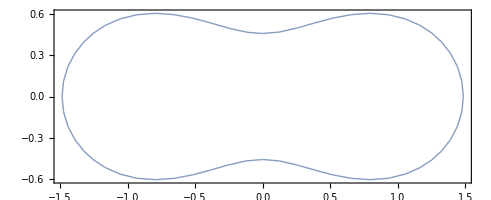

```mathematica
cassiniF[x1_,x2_,a_:1,b_:11/10]:=(x1^2+x2^2)^2 - 2 a^2 (x1^2 -x2^2)+a^4-b^4;
cassiniOval = ImplicitRegion[cassiniF[x,y]==0,{x,y}];
Region[cassiniOval,PlotRange->All,Frame->True]
```

```mathematica
Reduce[Element[{x,y},cassiniOval]]
```

(y==-121/200&&(x==-(√25359)/200||x==(√25359)/200))||(-121/200<y≤-(√21)/10&&(x==-√(1-y^2+1/100 √(14641-40000 y^2))||x==-√(1-y^2-1/100 √(14641-40000 y^2))||x==√(1-y^2-1/100 √(14641-40000 y^2))||x==√(1-y^2+1/100 √(14641-40000 y^2))))||(-(√21)/10<y<(√21)/10&&(x==-√(1-y^2+1/100 √(14641-40000 y^2))||x==√(1-y^2+1/100 √(14641-40000 y^2))))||((√21)/10≤y<121/200&&(x==-√(1-y^2+1/100 √(14641-40000 y^2))||x==-√(1-y^2-1/100 √(14641-40000 y^2))||x==√(1-y^2-1/100 √(14641-40000 y^2))||x==√(1-y^2+1/100 √(14641-40000 y^2))))||(y==121/200&&(x==-(√25359)/200||x==(√25359)/200))

```mathematica
Solve[(Cos[the]^2+b^2Sin[the]^2)^2 - 2 aa^2 (Cos[the]^2 - b^2Sin[the]^2) + aa^4 - bb^4 == 0, b]
```

{{b→-√(-Cot[the]^2-aa^2 Csc[the]^2-Csc[the]^4 √((2 aa^2+bb^4+2 aa^2 Cos[2 the]) Sin[the]^4))},{b→√(-Cot[the]^2-aa^2 Csc[the]^2-Csc[the]^4 √((2 aa^2+bb^4+2 aa^2 Cos[2 the]) Sin[the]^4))},{b→-√(-Cot[the]^2-aa^2 Csc[the]^2+Csc[the]^4 √((2 aa^2+bb^4+2 aa^2 Cos[2 the]) Sin[the]^4))},{b→√(-Cot[the]^2-aa^2 Csc[the]^2+Csc[the]^4 √((2 aa^2+bb^4+2 aa^2 Cos[2 the]) Sin[the]^4))}}